```mathematica
CoeffVector[prob_]:=Table[Coefficient[ prob,v,1],{v,Sort[myVars,SymbolComp2]}]
```

```mathematica
vectors=Table[CoeffVector[newAssoc[key]["colofour"]],{key,Keys[newAssoc]}];MatrixForm[vectors]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 2/3 | -1/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | 2/3 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | 2/3 | 0 | -1/6 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
2/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
2/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0
-1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
-1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
-1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 2/3 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1
-1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
-1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 2/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
-1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 2/3 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
-1/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 2/3 | 0 | 0 | 0 | 0
1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 2/3 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | 2/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
-1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | 2/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | -1/3 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
2/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
-1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 2/3 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0
1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0
1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | -1/3 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 2/3 | 0 | -1/6 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | -1/3 | 2/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 2/3 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/3 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | -1/3 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | 2/3 | 0 | -1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/3 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
-1/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/3 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -2/3 | 1/3 | 0 | 0 | 0 | -2/3 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 2/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
-1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | -1/3 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | -1/3 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | -2/3 | -2/3 | 0 | 1/6 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | 1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | -1/3 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 1/6 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | -1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0
1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/3 | 0 | 0 | 0 | 0
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/3 | 1/3 | -2/3 | 0 | 0 | 0 | 1/3 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
-1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1
-1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0
1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | -1/3 | -1/3 | 0 | 0 | 0 | -1/3 | 0 | -1/3 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | -1/3 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 2/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 2/3 | -1/3 | 0 | -1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0
0 | 0 | 1/3 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
1/4 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | 1/8 | 1/8 | -1/24 | 1/8 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | 5/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | -1/24 | -1/24 | 1/8 | 0
-1/12 | -1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 5/12 | -1/12 | -5/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | 1/12 | -1/12 | 1/12 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/8 | 1/8 | -1/24 | 1/8 | -1/24 | 0
1/6 | -1/6 | 1/6 | 0 | 1/6 | 0 | -1/6 | 1/6 | 1/2 | -1/6 | 1/3 | -1/6 | -1/3 | 0 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | -1/6 | 1/3 | 1/6 | 0 | 0 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/6 | -1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 0 | 1/6 | 0 | 1/4 | 1/4 | -1/12 | 1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | 1/12 | -1/4 | 1/12 | -5/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | 1/12 | -1/12 | -1/4 | 5/12 | -1/12 | 5/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | -5/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | -1/24 | -1/24 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | 5/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | -1/24 | -1/24 | 1/8 | 0
-1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | 5/12 | -1/12 | 1/12 | -5/12 | 1/12 | -1/12 | 5/12 | -5/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/8 | 1/8 | -1/24 | -1/24 | -1/24 | 0
1/6 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/2 | -1/6 | 1/3 | -1/6 | 1/6 | -1/3 | 0 | -1/6 | 1/3 | -1/3 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/4 | 1/4 | -1/12 | -1/12 | 1/12 | 0
1/3 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0
2/3 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 1/3 | 0
1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -5/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/24 | 1/8 | -1/24 | 1/8 | 1/8 | 0
1/2 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | -1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/12 | 1/4 | -1/12 | 1/12 | 1/4 | 0
1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | -5/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/12 | 1/12 | 5/12 | -1/24 | 11/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | -1/24 | -1/24 | 1/8 | 0
1/2 | 0 | -1/6 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | -1/3 | -1/3 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | 1/6 | 1/3 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | 1/12 | 1/4 | -1/12 | -1/12 | 1/4 | 0
1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | -1/4 | -1/4 | -5/12 | 1/12 | 1/12 | 1/4 | -1/4 | 1/12 | 1/12 | 1/12 | 1/4 | 1/4 | 1/12 | 1/12 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 3/8 | -1/8 | 1/24 | 1/24 | 0
1/3 | 0 | 0 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 1/3 | -1/3 | 0 | -1/3 | -1/6 | -1/3 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | 1/6 | 0 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/2 | -1/6 | 0 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/3 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 2/3 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 0
-1/4 | -1/12 | 1/12 | 1/12 | 5/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | 5/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/4 | 1/12 | -1/12 | 5/12 | 1/12 | 1/24 | -1/8 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 0 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
-1/12 | -1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 5/12 | 1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/8 | 1/8 | -1/24 | 1/8 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | 5/12 | 5/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 1/12 | -5/12 | -1/24 | -1/24 | 11/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/8 | 1/8 | -1/24 | -1/24 | -1/24 | 0
-1/12 | -1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 5/12 | -1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/8 | 1/8 | -1/24 | 1/8 | -1/24 | 0
-1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/2 | -1/6 | 1/3 | 1/3 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/3 | 0 | -1/3 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/4 | 1/4 | -1/12 | 1/12 | -1/12 | 0
0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | -1/12 | -1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/24 | 1/8 | -1/24 | 1/8 | 1/8 | 0
0 | 0 | 2/3 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0
1/6 | 0 | 1/2 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | 1/3 | 0 | 0 | -1/6 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/3 | -1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | 1/12 | 1/4 | -1/12 | 1/4 | 1/12 | 0
-1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | 5/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -5/12 | -1/24 | 11/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | -1/24 | 1/8 | -1/24 | 1/8 | -1/24 | 0
1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/4 | -1/4 | 1/12 | 1/12 | 1/12 | -1/4 | 1/4 | 1/12 | 1/12 | 1/12 | 1/4 | -1/4 | 1/12 | -5/12 | -1/8 | 3/8 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 3/8 | -1/8 | 1/24 | 1/24 | 0
-1/6 | 0 | 1/2 | 1/6 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | -1/3 | 1/3 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | 1/3 | 1/6 | -1/6 | -1/3 | -1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 1/12 | 1/4 | -1/12 | 1/4 | -1/12 | 0
0 | 0 | 1/3 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/3 | -1/3 | 0 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | 0 | 1/6 | -1/6 | 0 | -1/3 | -1/6 | 1/3 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 1/2 | -1/6 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -5/12 | 5/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -5/12 | 1/12 | 5/12 | -1/24 | -1/24 | 11/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | -1/24 | -1/24 | 1/8 | 0
-1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 1/12 | 5/12 | 1/12 | 1/12 | 5/12 | -5/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | -1/24 | 1/8 | -1/24 | 1/8 | -1/24 | 0
1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | -5/12 | 1/4 | 1/4 | 1/12 | 1/12 | 1/12 | 1/4 | -1/4 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | 1/12 | 1/12 | -1/8 | -1/8 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 3/8 | -1/8 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | -1/3 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | -1/3 | 1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 1/12 | 1/4 | -1/12 | -1/12 | 1/12 | 0
-1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | 0 | -1/6 | 1/6 | 0 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 0
0 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 1/3 | -1/3 | 0 | 1/6 | 1/3 | -1/3 | 1/6 | 0 | 1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/3 | -1/6 | 1/6 | -1/3 | -1/6 | -1/6 | 1/3 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 0 | 1/6 | -1/3 | 1/3 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 1/2 | -1/6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | -5/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/24 | 1/8 | -1/24 | 1/8 | 1/8 | 0
1/2 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/6 | -1/6 | -1/6 | -1/3 | 1/3 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/12 | 1/4 | -1/12 | 1/12 | 1/4 | 0
1/6 | 1/6 | 1/2 | 0 | -1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/6 | -1/3 | -1/6 | 1/6 | 1/3 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 0 | -1/12 | 1/4 | -1/12 | 1/4 | 1/12 | 0
1/3 | 1/6 | 1/3 | 0 | -1/6 | 0 | 1/6 | -1/6 | 0 | -1/3 | -1/3 | 1/6 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/6 | 0 | 0 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | -1/6 | 0 | 0 | 1/2 | -1/6 | 1/6 | 1/6 | 0
1/6 | 1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | -1/3 | -1/6 | -1/3 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | 1/6 | 0 | 0 | -1/12 | 5/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | 0
1/3 | 1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | -1/3 | -1/3 | 1/6 | -1/6 | -1/3 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 1/3 | 1/3 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 1/3 | -1/3 | -1/6 | 0 | 0 | 0 | 0 | 1/2 | -1/6 | 0 | 1/6 | 0
0 | 1/6 | 1/3 | 1/6 | -1/6 | 0 | -1/6 | 0 | 0 | -1/3 | -1/3 | -1/3 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 1/3 | 0 | -1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 0 | 1/6 | 0 | 0 | 1/3 | 0 | -1/6 | -1/3 | -1/6 | 1/6 | 0 | 1/2 | -1/6 | 1/6 | 0 | 0
1/6 | 1/6 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2 | -1/3 | 0 | 0 | -1/3 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 1/6 | -1/3 | -1/4 | 1/4 | 1/4 | -1/4 | 3/4 | -1/4 | -1/4 | -1/4 | -1/4 | 1/4 | -1/6 | 1/6 | 1/6 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/12 | 3/4 | -1/4 | 1/12 | 1/12 | 0
1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 5/12 | 1/24 | -11/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | -1/12 | -1/12 | -1/4 | -1/4 | 1/4 | 5/12 | 1/4 | -1/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 1/3 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | -1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | -1/3 | -1/6 | -1/6 | 1/3 | 1/12 | -5/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 0 | 0 | -1/6 | 0 | -1/3 | 1/6 | 1/3 | 1/6 | 0 | -1/6 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -5/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -1/12 | -1/12 | -1/12 | 1/4 | -1/4 | -1/4 | -1/12 | 1/4 | 5/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
-1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | 5/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | -1/8 | 1/24 | 1/24 | -1/8 | 0
-1/6 | -1/6 | 1/6 | 0 | 1/3 | -1/6 | 0 | 0 | 1/6 | 1/6 | 1/3 | 1/6 | -1/6 | 1/3 | 0 | -1/6 | -1/3 | 1/3 | -1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/6 | 0 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 0 | -1/6 | -1/6 | 1/6 | -1/3 | 0 | 0 | 1/6 | 1/3 | 0 | 1/12 | -1/4 | 1/12 | 1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 2/3 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0
1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -5/12 | -1/12 | -5/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 5/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/24 | -1/8 | 1/24 | -1/8 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | 5/12 | -5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 5/12 | 1/24 | 1/24 | -11/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 5/12 | -1/12 | -1/12 | 1/4 | -1/4 | 1/4 | -1/12 | -1/4 | -1/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/24 | -1/8 | 1/24 | -1/8 | 1/24 | 0
1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | 0 | 1/3 | 1/6 | 1/6 | 1/3 | -1/3 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/3 | 0 | 1/3 | 1/12 | 1/12 | -5/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/3 | -1/6 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/6 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 1/12 | -5/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | -1/4 | 3/4 | -1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/24 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | -1 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 2/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | -1/3 | -1/3 | 0 | 2/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 1/12 | 5/12 | -1/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | -1/24 | -1/24 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | 5/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | -1/24 | -1/24 | 1/8 | 0
-1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 5/12 | -1/12 | 1/12 | -5/12 | 1/12 | -1/12 | 5/12 | -5/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/8 | 1/8 | -1/24 | -1/24 | -1/24 | 0
1/6 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 1/3 | -1/6 | 1/6 | -1/3 | 0 | -1/6 | 1/3 | -1/3 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/4 | 1/4 | -1/12 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | -1/24 | -1/24 | 1/8 | 0
0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | 0 | 1/3 | 0 | 1/3 | 0 | 0 | 1/6 | 0 | 0 | 0
1/4 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | 1/8 | 1/8 | 1/8 | -1/24 | 1/8 | 0
-1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -5/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | 1/8 | -1/24 | -1/24 | 0
1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | 1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | -1/6 | -1/6 | 0 | -1/3 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 1/4 | 1/4 | 1/12 | -1/12 | 1/12 | 0
1/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -5/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 5/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/6 | 0
2/3 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/3 | 0
1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -5/12 | -5/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | -1/24 | -1/24 | 1/8 | 0
1/2 | 0 | -1/6 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | 1/6 | 1/3 | 0 | -1/6 | -1/3 | -1/3 | -1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | 1/12 | 1/4 | -1/12 | -1/12 | 1/4 | 0
1/4 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 5/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/24 | 1/8 | 1/8 | -1/24 | 1/8 | 0
1/2 | -1/6 | -1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | 0 | 1/6 | -1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/12 | 1/4 | 1/12 | -1/12 | 1/4 | 0
1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | 1/4 | -5/12 | -1/4 | 1/12 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | 3/8 | -1/8 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/24 | 3/8 | 1/24 | -1/8 | 1/24 | 0
1/3 | -1/6 | -1/3 | -1/6 | 0 | 1/6 | 0 | 1/6 | 1/3 | 0 | 0 | -1/3 | 1/6 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/6 | 1/2 | 0 | -1/6 | 1/6 | 0
-1/3 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | -1/3 | 0 | 1/6 | 2/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 0
-1/4 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -5/12 | -1/12 | -5/12 | -1/12 | -1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/4 | 1/12 | 5/12 | -1/12 | 1/12 | 1/24 | -1/8 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 5/12 | 1/12 | -5/12 | 1/12 | 5/12 | -1/12 | 1/12 | 1/12 | -5/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/8 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 1/3 | 0 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 0 | 0
-1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | 5/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | 1/8 | -1/24 | -1/24 | 0
-1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | 1/8 | -1/24 | -1/24 | 0
-1/6 | 1/6 | -1/6 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/2 | 1/6 | -1/6 | 1/3 | 0 | -1/3 | 1/6 | 1/3 | -1/6 | 0 | 1/6 | -1/3 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/6 | 1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | -1/6 | 0 | 1/4 | 1/4 | 1/12 | -1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -5/12 | -1/12 | -5/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | -1/24 | -1/24 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | -1/3 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | -1/3 | 1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 1/12 | 1/4 | -1/12 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -5/12 | -1/12 | -1/12 | -5/12 | 1/12 | 1/12 | 5/12 | 5/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | 1/8 | -1/24 | -1/24 | 0
1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | -5/12 | -1/4 | 1/12 | -1/4 | 1/12 | 1/12 | 1/4 | 1/12 | 1/4 | 1/12 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/24 | 3/8 | 1/24 | -1/8 | 1/24 | 0
-1/6 | -1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 1/6 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 11/12 | -1/12 | -1/12 | 0 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 0
0 | -1/6 | -1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/3 | 1/6 | -1/6 | -1/3 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 5/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | -1/3 | 0 | 0 | 1/6 | 1/3 | 0 | 0 | 1/6 | 1/2 | 0 | -1/6 | 0 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 5/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -5/12 | 5/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -11/24 | 1/24 | 1/24 | -1/12 | 5/12 | -1/12 | 1/4 | 1/4 | -1/4 | -1/12 | -1/4 | -1/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | -1/6 | 0 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | 0 | -1/6 | 0 | 1/3 | 0 | 0 | 1/6 | 0 | 0 | 0
1/4 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | 5/12 | -1/12 | -5/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | 1/12 | -1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/24 | 1/8 | 1/8 | -1/24 | 1/8 | 0
-1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 5/12 | -1/12 | 1/12 | -5/12 | 1/12 | -1/12 | 5/12 | -5/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | 1/8 | -1/24 | -1/24 | 0
1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | 1/4 | 1/12 | 1/4 | -5/12 | 1/12 | -1/4 | 1/12 | -1/4 | 1/12 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/24 | 3/8 | 1/24 | -1/8 | 1/24 | 0
0 | 1/6 | 0 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 2/3 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | 0 | 1/3 | 0 | 0 | 0
1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | -1/6 | 1/6 | 1/2 | 0 | 1/3 | -1/6 | -1/3 | 0 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | -1/6 | 1/3 | 1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | 1/12 | 1/4 | 1/4 | -1/12 | 1/12 | 0
-1/6 | 1/6 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/2 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 1/3 | -1/6 | 1/6 | -1/3 | 0 | -1/6 | 1/3 | -1/3 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 1/12 | 1/4 | 1/4 | -1/12 | -1/12 | 0
0 | 1/6 | -1/3 | -1/6 | 0 | 0 | 1/6 | -1/6 | 1/3 | 1/3 | 0 | 1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 0 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/6 | 1/2 | 1/6 | -1/6 | 0 | 0
1/4 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -1/12 | 5/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/24 | 1/8 | 1/8 | -1/24 | 1/8 | 0
1/2 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/3 | 0 | -1/3 | -1/6 | -1/3 | -1/6 | 0 | 1/6 | 1/3 | 1/6 | -1/6 | 0 | 1/6 | -1/6 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/12 | 1/4 | 1/12 | -1/12 | 1/4 | 0
1/6 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | 0 | 1/6 | -1/6 | 0 | -1/3 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | 5/12 | -1/12 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/12 | 1/4 | 1/12 | -1/12 | 1/12 | 0
1/3 | 0 | -1/3 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/3 | 1/6 | 1/6 | 1/3 | 0 | 1/6 | -1/3 | -1/3 | -1/6 | 0 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | 1/3 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/3 | 0 | 1/3 | 1/6 | -1/6 | 0 | 1/2 | 0 | -1/6 | 1/6 | 0
1/12 | -1/12 | 1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 5/12 | 5/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -11/24 | 1/24 | -1/12 | -1/12 | -1/12 | -1/4 | 1/4 | 1/4 | -1/12 | -1/4 | -1/12 | 5/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | 0 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 1/6 | 0 | -1/3 | -1/6 | -1/6 | -1/3 | 0 | 1/6 | 1/3 | 1/3 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | -1/12 | 1/4 | 1/4 | -1/12 | 1/12 | 0
1/3 | -1/6 | -1/3 | 1/6 | 1/6 | 0 | 0 | -1/6 | 0 | 1/3 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/3 | -1/3 | 0 | -1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 1/2 | 1/6 | -1/6 | 1/6 | 0
0 | -1/6 | -1/3 | -1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 1/3 | 1/6 | -1/3 | 0 | 1/3 | 1/6 | -1/3 | 1/6 | 0 | -1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 5/6 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | -1/3 | 0 | 1/6 | 1/3 | 1/6 | -1/6 | 0 | 1/2 | 1/6 | -1/6 | 0 | 0
1/6 | -1/6 | -1/2 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | -1/3 | 1/6 | 0 | -1/3 | 0 | 1/6 | -1/4 | -1/4 | 1/4 | -1/4 | -1/4 | -1/4 | 1/4 | 3/4 | 1/4 | -1/4 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/2 | 1/6 | -1/6 | 1/12 | 3/4 | 1/12 | -1/4 | 1/12 | 0
1/6 | 0 | 1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | -1/3 | -1/6 | -1/6 | 1/3 | 0 | 1/6 | 1/3 | 1/3 | -1/6 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | -5/12 | 1/12 | 0 | 0 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 0
-1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | -1/8 | 1/24 | 1/24 | -1/8 | 0
-1/6 | 1/3 | 1/6 | 0 | -1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 0 | 1/3 | 1/6 | -1/6 | 1/3 | 0 | -1/6 | -1/3 | 1/3 | -1/6 | 0 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | -5/12 | 1/12 | 1/12 | 0 | 1/3 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/3 | -1/6 | 0 | 1/12 | -1/4 | 1/12 | 1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -5/12 | -1/12 | 5/12 | -1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 5/12 | -1/12 | -1/12 | 1/4 | -1/4 | 1/4 | -1/12 | -1/4 | -1/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 0 | -1/3 | 0 | 2/3 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 0
1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | 1/12 | -1/4 | -1/12 | -5/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 5/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 1/24 | -1/8 | -1/8 | 1/24 | 1/24 | 0
1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/24 | -1/8 | -1/8 | 1/24 | 1/24 | 0
1/6 | 0 | 1/6 | 0 | -1/6 | 0 | -1/6 | 1/3 | 1/6 | -1/6 | -1/6 | -1/3 | 0 | 1/3 | -1/6 | 1/3 | 1/6 | 0 | -1/6 | 1/3 | -1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/3 | 0 | 0 | 1/6 | 0 | 1/6 | -1/6 | -1/3 | -1/6 | 0 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 0
-1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -5/12 | -1/12 | 1/12 | 1/12 | -5/12 | 1/12 | -1/12 | -5/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | -1/4 | 1/12 | 3/4 | 1/12 | 1/12 | -1/24 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | -1/3 | 0 | 0 | 1/6 | 0 | 0 | 2/3 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 2/3 | 1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
-1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/6 | 0
1/6 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/3 | 0
-1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | 1/4 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/8 | -1/24 | -1/24 | 1/8 | 1/8 | 0
1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 0 | 1/6 | 1/2 | 1/6 | 0 | -1/6 | 0 | 1/6 | 0 | -1/6 | 1/3 | 0 | 1/6 | 0 | 1/3 | -1/6 | 0 | -1/3 | 0 | -1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/4 | 1/12 | -1/12 | 1/12 | 1/4 | 0
-1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 5/12 | 1/12 | -5/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -5/12 | 5/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | -1/24 | -1/24 | 1/8 | 0
1/6 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/6 | 1/2 | 1/6 | 0 | 1/3 | 0 | -1/3 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/4 | 1/12 | -1/12 | -1/12 | 1/4 | 0
-1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | 1/4 | 1/12 | 1/4 | -5/12 | 1/12 | -1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 3/8 | 1/24 | -1/8 | 1/24 | 1/24 | 0
1/6 | -1/3 | -1/6 | 0 | 0 | 1/6 | -1/6 | 1/3 | 1/3 | 0 | 1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 0 | -1/6 | 1/6 | 0 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/2 | 1/6 | -1/6 | 0 | 1/6 | 0
-1/6 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0
1/6 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 1/3 | 0
-1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 1/12 | -5/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -5/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | -1/24 | -1/24 | 1/8 | 0
1/6 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/6 | 1/2 | 1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/3 | 0 | -1/3 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | -1/3 | 1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/4 | 1/12 | -1/12 | -1/12 | 1/4 | 0
-1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 5/12 | 1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/8 | -1/24 | 1/8 | -1/24 | 1/8 | 0
1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 1/2 | 1/6 | -1/6 | 1/3 | 0 | 0 | -1/3 | -1/6 | -1/6 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 0 | 1/6 | 1/3 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/4 | 1/12 | 1/12 | -1/12 | 1/4 | 0
-1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | -5/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/4 | 1/12 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 3/8 | 1/24 | 1/24 | -1/8 | 1/24 | 0
1/6 | 0 | 0 | -1/6 | -1/3 | 1/6 | 0 | 1/3 | 1/3 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 0 | 1/6 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/2 | 1/6 | 0 | -1/6 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0
1/3 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 2/3 | 0
-1/3 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 0
1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/4 | -5/12 | 1/4 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | 3/8 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/24 | 1/24 | -1/8 | 1/24 | 3/8 | 0
1/3 | 0 | -1/6 | -1/3 | -1/6 | 1/6 | 0 | 1/3 | 1/6 | 0 | 0 | 0 | 1/3 | 1/6 | -1/3 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | -1/3 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | 1/6 | -1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 1/2 | 0
1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -5/12 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | -1/4 | 1/4 | 1/12 | 1/12 | 1/12 | 1/4 | 1/4 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | -1/8 | 3/8 | 0
1/3 | -1/6 | 0 | 0 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | -1/6 | 0 | 0 | -1/3 | -1/6 | -1/3 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | 1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/2 | 0
1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -7/24 | 5/24 | -7/24 | -7/24 | 5/24 | -7/24 | 5/24 | 5/24 | 5/24 | 5/24 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 5/24 | 5/24 | -1/8 | -1/8 | 5/24 | 0
1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | -1/6 | -1/6 | 1/3 | 0
-1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/8 | -1/8 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | 1/12 | 5/12 | 1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -5/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/8 | -1/24 | -1/24 | 1/8 | -1/24 | 0
0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | 0 | 1/6 | 1/3 | 0 | 1/6 | 0 | -1/3 | -1/6 | 0 | -1/3 | 0 | 1/6 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/4 | 1/12 | -1/12 | 1/12 | -1/12 | 0
1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -5/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -5/12 | -1/24 | -1/24 | 11/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | 1/8 | -1/24 | -1/24 | 0
0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 1/3 | 0 | 0 | -1/3 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/12 | -1/12 | 11/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | 1/12 | -1/12 | -1/12 | 0
1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/4 | -5/12 | 1/12 | 1/12 | 1/4 | 1/4 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | -1/4 | -1/8 | -1/8 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 3/8 | 1/24 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/3 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/3 | 0 | -1/3 | 1/6 | -1/6 | -1/6 | -1/6 | 5/6 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | 1/3 | -1/3 | 1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 1/2 | 1/6 | 0 | 0 | -1/6 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | -5/12 | -1/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
-1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 5/12 | -1/12 | -5/12 | 1/12 | 1/12 | -1/12 | 5/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | 1/8 | 1/8 | 0
1/6 | 1/6 | -1/6 | -1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 0 | 1/6 | 0 | -1/6 | -1/3 | 0 | 1/6 | 0 | 1/3 | 1/6 | 0 | -1/3 | 0 | -1/6 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 0 | -1/6 | 1/6 | 0 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/12 | 1/12 | -1/12 | 1/12 | 1/4 | 0
0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/6 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/12 | -1/12 | -1/12 | 1/4 | 1/12 | 0
1/6 | 0 | -1/3 | 0 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | -1/6 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | -1/6 | -1/6 | 0 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 0 | 1/3 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/6 | 1/3 | 1/3 | -1/6 | 1/3 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/3 | 0 | 1/3 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/3 | -1/3 | -1/4 | 1/4 | 3/4 | -1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/4 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 1/12 | 1/4 | -1/12 | -1/12 | 1/12 | 0
0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | -1/3 | -1/6 | 1/6 | 1/3 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 3/4 | -1/4 | -1/4 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/4 | 1/12 | -1/12 | 1/12 | -1/12 | 0
1/6 | -1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | 1/3 | -1/6 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/2 | -1/6 | -1/6 | 0 | 0 | -1/2 | 1/3 | -1/6 | -1/3 | 1/6 | 2/3 | -1/3 | 1/6 | -1/3 | 1/6 | 2/3 | -1/3 | -1/3 | -1/6 | 0 | 1/3 | -1/3 | 1/6 | -1/6 | 1/6 | 1/3 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | 0 | 0 | 0
-1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | -5/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | 5/12 | -1/24 | -1/24 | 11/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | -1/24 | -1/24 | 1/8 | -1/24 | 1/8 | 0
1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/3 | 0 | 0 | -1/3 | -1/6 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | -1/12 | -1/12 | 11/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/3 | -1/3 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/4 | -1/4 | 3/4 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 1/12 | 1/4 | -1/12 | -1/12 | 1/12 | 0
0 | 1/6 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | -1/3 | -1/6 | -1/3 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | 1/6 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 0
1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | 5/6 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 0
0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | -1/3 | 1/6 | -1/6 | 1/3 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/4 | -1/4 | 1/4 | -1/4 | 3/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | 1/12 | -1/12 | -1/12 | 0
1/6 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | -1/3 | 1/3 | -1/3 | 0 | 0 | 1/3 | -1/2 | 1/3 | 0 | 0 | -1/6 | 1/2 | -1/6 | 0 | 0 | -1/6 | 0 | -1/6 | -1/3 | -1/3 | 2/3 | -1/3 | 2/3 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/3 | 1/3 | -1/6 | -1/6 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0
1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | -1/4 | -5/12 | 1/12 | 1/12 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | 1/4 | 1/4 | 1/12 | 1/12 | 1/12 | 1/4 | -1/8 | -1/8 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/8 | 1/24 | 1/24 | 1/24 | 3/8 | 0
1/3 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | -1/3 | -1/3 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 1/3 | 0 | -1/3 | 1/6 | 1/6 | -1/6 | -1/6 | 5/6 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | 0 | 1/3 | 0 | 1/6 | -1/3 | -1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | 1/2 | 0
-1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -5/12 | -1/12 | 5/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | -1/8 | 1/24 | 1/24 | -1/8 | 0
1/6 | 1/6 | -1/6 | -1/6 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/3 | 1/3 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | 1/3 | 1/6 | -1/6 | -1/3 | 0 | -1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | 3/4 | 1/4 | 1/4 | 0 | -1/6 | 1/6 | 0 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/12 | 1/12 | -1/12 | 1/12 | 1/4 | 0
1/3 | 1/6 | -1/3 | -1/6 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | -1/6 | -1/6 | 0 | 1/2 | -1/6 | 0 | -1/6 | 0 | 0 | 1/3 | 0 | 1/3 | 0 | -1/2 | -1/6 | 0 | -1/3 | -1/3 | 2/3 | -1/3 | 1/6 | -1/3 | -1/3 | 2/3 | 1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 1/6 | -1/3 | -1/6 | 1/3 | 1/6 | 0 | 0 | 1/3 | -1/6 | 0 | 1/3 | 0
1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | -1/3 | -1/3 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | 1/6 | 1/3 | 0 | -1/4 | 1/4 | 1/4 | -1/4 | 3/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 0
1/3 | 0 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/3 | 1/6 | -1/3 | -1/6 | 0 | -1/6 | -1/2 | 0 | -1/6 | 0 | 1/3 | 0 | 0 | 1/3 | 0 | -1/6 | 1/2 | 0 | -1/3 | 1/6 | 2/3 | -1/3 | 2/3 | -1/3 | 1/6 | 1/6 | -1/3 | -1/3 | -1/6 | 1/6 | 1/3 | -1/6 | 1/3 | -1/3 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/3 | 0 | -1/6 | 1/3 | 0
1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/6 | -1/3 | 0 | 0 | 1/3 | -1/6 | 1/6 | 0 | 0 | -1/6 | 1/3 | 1/6 | 0 | 0 | -1/6 | -5/12 | 1/12 | 1/12 | -5/12 | 7/12 | -5/12 | 1/12 | 7/12 | 1/12 | 1/12 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 1/12 | 1/4 | -1/12 | -1/12 | 1/12 | 0
1/3 | 0 | -1/3 | 0 | 0 | 1/3 | 0 | -1/3 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/3 | 0 | -1/3 | 1/6 | -1/6 | -1/2 | 0 | 1/2 | -1/2 | 1/2 | -1/2 | 0 | 1/2 | 0 | 0 | -1/3 | 0 | 1/3 | -1/3 | 1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 1/6 | 1/2 | -1/6 | -1/6 | 1/6 | 0
-1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | 0 | -1/3 | -1/6 | 1/3 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 0 | 1/6 | 1/3 | -1/6 | 0 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | -1/12 | -1/4 | 1/12 | 1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -5/12 | -1/12 | 5/12 | -1/12 | -1/12 | 1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | -1/4 | 1/4 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/4 | -1/12 | 1/4 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 0
0 | -1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 5/6 | 0 | 0 | -1/6 | 0 | -1/6 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 1/3 | -1/6 | 0 | 1/3 | 0 | -1/6 | 1/12 | 1/12 | -11/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/2 | -1/6 | 1/6 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 0
-1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 5/12 | 5/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 5/12 | 1/24 | 1/24 | -11/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/4 | -1/12 | -1/12 | -1/12 | -1/4 | -1/12 | 1/4 | 5/12 | 1/4 | -1/12 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | 5/6 | 0 | 1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/6 | 1/3 | 1/12 | 1/12 | -11/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 0
-1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 1/4 | 5/12 | -1/12 | -1/12 | -1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/4 | -1/12 | -1/12 | -1/12 | 1/4 | 1/8 | 1/8 | -3/8 | 1/8 | -3/8 | 1/8 | 1/8 | -3/8 | 1/8 | 1/8 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | -1/24 | -1/24 | 1/8 | 0
0 | -1/6 | 1/6 | -1/6 | -1/6 | 0 | -1/6 | 2/3 | 0 | 1/6 | 1/6 | 0 | -1/6 | 1/3 | -1/3 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/3 | 0 | 1/3 | -1/6 | 1/6 | 1/6 | 1/6 | -5/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/3 | 0 | -1/3 | 1/3 | -1/3 | 1/3 | 0 | -1/3 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 0
-1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -5/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -5/12 | 1/12 | 1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -5/12 | 1/12 | 1/12 | -1/4 | 1/4 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/24 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 2/3 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | -1/3 | 1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/6 | 0
1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 5/12 | -5/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -5/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | 5/12 | -1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/8 | 1/24 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -5/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 5/12 | 1/24 | 1/24 | -11/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | 5/12 | -1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/4 | -1/8 | 1/24 | 1/24 | 1/24 | 1/24 | 0
1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -5/12 | 1/24 | 1/24 | -11/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | -1/4 | -1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | -1/6 | 0 | 0 | -1/6 | 0 | 1/6 | 0 | 5/6 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/12 | 1/12 | -5/12 | 1/12 | -11/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/6 | 1/6 | -1/2 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | -5/12 | -5/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | -5/12 | -1/24 | -1/24 | 11/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | -1 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 2/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
1/6 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | 2/3 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/6 | 0
1/12 | 1/12 | 5/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | -1/12 | -5/12 | 1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | -1/12 | 5/12 | 1/12 | 5/12 | -1/12 | -1/8 | 1/24 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -5/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | -1/12 | -1/12 | -1/4 | 1/4 | -1/12 | -1/12 | -1/4 | -1/12 | 5/12 | 1/4 | -1/8 | 1/24 | 1/24 | 1/24 | 1/24 | 0
1/12 | -1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | 1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | -1/12 | 1/4 | -1/4 | -1/12 | -1/12 | 1/4 | 5/12 | -1/12 | -1/4 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 0
0 | 0 | 5/6 | 0 | 0 | -1/6 | 0 | 1/6 | 0 | -1/6 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | -11/12 | 1/12 | 1/12 | -1/6 | 1/6 | -1/2 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | -5/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | -1 | 0 | -1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 2/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | -1/3 | 2/3 | 0 | -1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 0 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
-1/12 | -1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 5/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/8 | 1/8 | -1/24 | 1/8 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 1/12 | -5/12 | 5/12 | 5/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/8 | 1/8 | -1/24 | -1/24 | -1/24 | 0
-1/12 | -1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -5/12 | -1/12 | 5/12 | 1/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/8 | 1/8 | -1/24 | 1/8 | -1/24 | 0
-1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/3 | 0 | -1/3 | 1/3 | 1/3 | 1/6 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/4 | 1/4 | -1/12 | 1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 1/12 | -5/12 | 1/12 | 5/12 | -1/12 | 1/12 | 1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/8 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 1/3 | 0 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 0 | 0
-1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | -5/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | 1/8 | -1/24 | -1/24 | 0
-1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | 1/8 | -1/24 | -1/24 | 0
-1/6 | 1/6 | -1/6 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/3 | 0 | -1/3 | 1/6 | 1/3 | -1/6 | 0 | 1/6 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/6 | 1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | -1/6 | 0 | 1/4 | 1/4 | 1/12 | -1/12 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | 5/12 | 1/12 | -5/12 | -1/12 | 1/12 | -1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 11/24 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | -1/24 | 1/8 | -1/24 | 1/8 | -1/24 | 0
-1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | 1/3 | -1/3 | 0 | 1/6 | 0 | -1/6 | 1/6 | 0 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | 5/12 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 0
-1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 1/12 | -5/12 | -5/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | -1/24 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | 1/8 | -1/24 | -1/24 | 0
-1/6 | -1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 1/6 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | 5/12 | -1/12 | -1/12 | -1/12 | 0 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 0
-1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/4 | -5/12 | 1/4 | 1/12 | 1/12 | -1/4 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/8 | 3/8 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 3/8 | 1/24 | 1/24 | -1/8 | 0
-1/3 | -1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | 0 | 1/3 | 0 | 0 | -1/3 | 1/6 | 1/6 | 1/3 | 0 | 1/6 | -1/3 | -1/3 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | 1/3 | -1/6 | -1/6 | 1/3 | 0 | -1/6 | 0 | -1/3 | 0 | 1/3 | 1/6 | 0 | -1/6 | 1/6 | 1/6 | 1/2 | 0 | 0 | -1/6 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 5/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 5/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 5/12 | 5/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -11/24 | 1/24 | 1/24 | 1/24 | -1/12 | 5/12 | -1/12 | 1/4 | 1/4 | -1/4 | -1/12 | -1/4 | -1/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 5/12 | -1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | -11/24 | -1/12 | -1/12 | -1/12 | 1/4 | -1/4 | -1/4 | -1/12 | 1/4 | 5/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/3 | 0 | 1/3 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
-1/12 | -1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 5/12 | 1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/8 | 1/8 | -1/24 | 1/8 | -1/24 | 0
0 | 1/3 | 0 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | -1/6 | 0 | 1/3 | 0 | -1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 0 | 0
-1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 1/4 | -1/12 | 5/12 | -1/12 | 1/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/12 | 1/12 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/8 | 1/8 | 1/8 | -1/24 | -1/24 | 0
-1/12 | 1/4 | 1/4 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/8 | 1/8 | 1/8 | 1/8 | -1/24 | 0
-1/6 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 1/2 | 1/6 | -1/6 | 1/3 | 0 | 0 | -1/3 | -1/6 | -1/6 | 0 | 0 | 1/6 | 1/3 | -1/6 | 0 | 0 | 1/6 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 1/4 | 1/4 | 1/12 | 1/12 | -1/12 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | -5/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/12 | -1/12 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | 1/12 | 5/12 | -1/4 | -1/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 1/3 | 0 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
-1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -5/12 | 1/12 | -1/12 | -5/12 | 5/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | -1/24 | 1/8 | -1/24 | 1/8 | -1/24 | 0
0 | 0 | 2/3 | 0 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0
-1/6 | 0 | 1/2 | 1/6 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | -1/6 | -1/3 | 0 | -1/6 | -1/3 | 1/3 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 1/12 | 1/4 | -1/12 | 1/4 | -1/12 | 0
-1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | -5/12 | 1/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/24 | 1/8 | 1/8 | 1/8 | -1/24 | 0
-1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | 1/12 | -1/4 | 1/12 | -1/4 | -5/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | 1/4 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/8 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 3/8 | 1/24 | 1/24 | -1/8 | 0
-1/6 | -1/6 | 1/2 | 0 | 1/6 | 1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/6 | 1/6 | 0 | -1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | 0 | -1/6 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 0 | -1/6 | 1/6 | 0 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 1/12 | 1/4 | 1/12 | 1/4 | -1/12 | 0
-1/3 | -1/6 | 1/3 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/3 | -1/3 | 0 | -1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/2 | 0 | 1/6 | -1/6 | 0
0 | 0 | -1/3 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | -1/3 | 2/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0
1/12 | 5/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | 5/12 | -1/12 | -5/12 | -1/12 | 1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | -1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/24 | -1/8 | 1/24 | -1/8 | 1/24 | 0
0 | -1/6 | 0 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 0 | 1/3 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 0 | 0
-1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 1/12 | 5/12 | -1/12 | 1/12 | -5/12 | 1/12 | -1/12 | 5/12 | -5/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/24 | 1/8 | 1/8 | -1/24 | -1/24 | 0
-1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/24 | 1/8 | 1/8 | 1/8 | -1/24 | 0
-1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | -5/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/4 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | 3/8 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/24 | 3/8 | 1/24 | 1/24 | -1/8 | 0
0 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 2/3 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | -1/3 | 0 | 0 | 1/3 | 0 | 0 | 0
-1/6 | 1/6 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/2 | 0 | 1/3 | -1/6 | 1/6 | -1/3 | 0 | -1/6 | 1/3 | -1/3 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 1/12 | 1/4 | 1/4 | -1/12 | -1/12 | 0
-1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/2 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | -1/6 | -1/6 | 0 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 1/12 | 1/4 | 1/4 | 1/12 | -1/12 | 0
-1/3 | 1/6 | 0 | 0 | -1/6 | -1/6 | 1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 0 | 1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/2 | 1/6 | 0 | -1/6 | 0
-1/12 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 5/12 | 1/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/24 | 1/8 | 1/8 | 1/8 | -1/24 | 0
-1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | 1/6 | 1/3 | 0 | 0 | -1/3 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/6 | 0 | 0 | 1/6 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | -1/12 | 1/4 | 1/12 | 1/12 | -1/12 | 0
1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | -1/12 | 5/12 | -1/4 | 1/4 | -1/4 | -1/12 | 1/4 | -1/12 | -1/12 | 1/24 | -1/8 | 1/24 | 1/24 | 1/24 | 0
-1/6 | 0 | 1/2 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | 1/3 | 0 | 1/3 | 1/6 | -1/3 | -1/6 | 0 | -1/6 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | -1/6 | -1/6 | -1/6 | 0 | -1/12 | 1/4 | 1/12 | 1/4 | -1/12 | 0
-1/3 | 0 | 1/3 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/3 | -1/3 | -1/3 | 1/6 | 0 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 1/3 | 0 | -1/3 | -1/6 | 1/6 | 0 | 1/2 | 0 | 1/6 | -1/6 | 0
-1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/3 | 0 | -1/3 | -1/3 | 1/3 | -1/6 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | -1/6 | -1/12 | 1/4 | 1/4 | 1/12 | -1/12 | 0
-1/3 | -1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | 1/3 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/3 | 0 | -1/3 | -1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 0 | -1/3 | 1/3 | 1/6 | 0 | 0 | 0 | 0 | 1/2 | 1/6 | 0 | -1/6 | 0
-1/3 | -1/6 | 1/3 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | 1/3 | 1/6 | -1/3 | 0 | 0 | 1/3 | 1/6 | 1/6 | 0 | 0 | -1/6 | -1/3 | 1/6 | 0 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | 1/3 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 1/2 | 1/6 | 1/6 | -1/6 | 0
-1/2 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | -1/3 | -1/3 | 0 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/4 | -1/4 | -1/4 | -1/4 | -1/4 | 3/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 1/6 | 1/12 | 3/4 | 1/12 | 1/12 | -1/4 | 0
1/6 | 0 | 1/6 | -1/6 | 0 | 1/3 | -1/6 | 0 | -1/6 | 1/6 | 0 | -1/3 | -1/6 | -1/6 | 1/3 | 0 | 1/6 | 1/3 | 1/3 | -1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/6 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 0 | 0 | 1/3 | 0 | 1/6 | -1/3 | -1/6 | 1/6 | 0 | -1/6 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 0
1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -5/12 | -1/12 | 5/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/24 | -1/8 | 1/24 | -1/8 | 1/24 | 0
1/6 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/3 | 0 | 1/3 | 1/3 | -1/3 | -1/6 | 0 | -1/6 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | -5/12 | 1/12 | 1/12 | 1/12 | -1/6 | 1/3 | 0 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | -1/6 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 0
0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 0 | 2/3 | 0 | -1/3 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 0
1/12 | 1/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -5/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 5/12 | -1/12 | -1/12 | 5/12 | 1/12 | 1/24 | -1/8 | -1/8 | 1/24 | 1/24 | 0
1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | 5/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/24 | -1/8 | -1/8 | 1/24 | 1/24 | 0
1/6 | 0 | 1/6 | 0 | 1/3 | 0 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/6 | -1/6 | -1/3 | 0 | 1/3 | -1/6 | 1/3 | 1/6 | 0 | -1/6 | 1/3 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | -5/12 | -1/6 | 0 | 0 | 1/6 | 0 | -1/3 | -1/6 | 1/6 | 1/3 | 0 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 0
-1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -5/12 | -5/12 | 1/12 | -5/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | 3/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/24 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/3 | 0 | 0 | 2/3 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 2/3 | 0 | 0 | -1/3 | 1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | 1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/6 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
-1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | 1/4 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | 5/12 | -1/12 | 5/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/8 | -1/24 | -1/24 | 1/8 | 1/8 | 0
0 | 0 | 1/6 | 0 | 2/3 | -1/3 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0
-1/6 | -1/6 | 1/6 | 0 | 1/2 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 0 | -1/3 | 1/3 | 0 | 1/3 | 0 | 1/6 | -1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 1/4 | 1/12 | -1/12 | 1/4 | 1/12 | 0
1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -5/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -5/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/8 | -1/24 | -1/24 | 1/8 | -1/24 | 0
-1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/4 | 1/12 | -1/4 | 1/12 | -5/12 | 1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 3/8 | 1/24 | -1/8 | 1/24 | 1/24 | 0
0 | -1/6 | 1/6 | 1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 0 | 1/3 | 0 | -1/3 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/4 | 1/12 | -1/12 | 1/4 | -1/12 | 0
-1/6 | -1/3 | 1/6 | 1/6 | 1/3 | 0 | -1/6 | 0 | 1/3 | 0 | 1/6 | 0 | -1/6 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | -1/3 | 1/6 | 0 | 1/3 | 0 | 1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | 1/2 | 1/6 | -1/6 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 1/12 | -5/12 | -1/12 | 5/12 | 1/12 | 1/12 | 1/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | -1/24 | -1/24 | 1/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 | -1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 1/6 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | -1/12 | -5/12 | 1/12 | -1/12 | -5/12 | 5/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | 1/8 | -1/24 | -1/24 | 0
-1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/4 | 1/12 | 1/12 | -1/4 | 1/12 | -1/4 | -5/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | 1/4 | 1/12 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 3/8 | 1/24 | 1/24 | -1/8 | 1/24 | 0
0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 1/3 | 0 | 0 | -1/3 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | 1/12 | -1/12 | -1/12 | 0
-1/6 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | 0 | 1/3 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/3 | 0 | -1/3 | -1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | 5/6 | -1/6 | -1/6 | 0 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | 1/3 | 1/2 | 1/6 | 0 | -1/6 | 0 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -5/12 | 5/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
-1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -5/12 | 1/12 | 5/12 | -1/12 | -5/12 | 1/12 | 1/12 | -1/12 | 5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 11/24 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | 1/8 | 1/8 | 0
-1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/3 | -1/3 | 0 | -1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | 5/12 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 0
-1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 0 | 1/6 | -1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 11/12 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | -1/12 | 1/12 | -1/12 | 1/4 | 1/12 | 0
-1/3 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | 5/6 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | 0 | -1/6 | 0 | 1/3 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 | -1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | -1/6 | -1/6 | 1/6 | 0 | -1/3 | -1/6 | -1/6 | -1/3 | 0 | 1/6 | 1/3 | 1/3 | 1/6 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 3/4 | 1/4 | -1/4 | -1/4 | 1/4 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 0
-1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/3 | 1/3 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | 1/6 | -1/6 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 3/4 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 0
-1/3 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/3 | -1/6 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | -1/2 | -1/6 | -1/6 | 0 | 0 | 1/2 | 1/3 | -1/6 | -1/3 | 1/6 | -1/3 | -1/3 | 1/6 | 2/3 | 1/6 | -1/3 | -1/3 | 2/3 | -1/6 | 0 | -1/6 | -1/3 | 1/6 | 1/3 | 1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/12 | 5/12 | 1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | -11/24 | -1/12 | 1/4 | 1/4 | -1/12 | 5/12 | -1/4 | -1/12 | -1/12 | -1/4 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 0
1/6 | -1/6 | 0 | 0 | 5/6 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | -11/12 | -1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/2 | -1/6 | 1/6 | 1/6 | -1/6 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 0
0 | 0 | -1/6 | 0 | 1/3 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0
1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -5/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -5/12 | -1/12 | 1/12 | 11/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/8 | -1/24 | -1/24 | 1/8 | -1/24 | 0
0 | 0 | 1/6 | 0 | 2/3 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0
0 | -1/6 | 1/6 | 1/6 | 1/2 | -1/6 | -1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | 1/3 | 0 | -1/3 | -1/6 | 1/6 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/4 | 1/12 | -1/12 | 1/4 | -1/12 | 0
1/12 | 1/4 | -1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 1/12 | -1/12 | 5/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/8 | -1/24 | 1/8 | 1/8 | -1/24 | 0
1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/4 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | 1/4 | 1/4 | 1/12 | -5/12 | 1/12 | -1/4 | 3/8 | -1/8 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 3/8 | 1/24 | 1/24 | 1/24 | -1/8 | 0
0 | 1/6 | 1/6 | 0 | 1/2 | 1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/3 | 0 | 0 | 1/3 | 1/6 | -1/6 | 0 | 0 | -1/6 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 1/4 | 1/12 | 1/12 | 1/4 | -1/12 | 0
0 | 0 | 1/6 | 1/6 | 1/3 | -1/6 | 0 | -1/3 | 1/3 | -1/6 | 1/6 | 0 | 1/6 | 0 | -1/6 | -1/3 | 0 | 1/6 | 0 | 1/3 | 1/6 | 0 | -1/3 | 0 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 1/2 | 1/6 | 0 | 1/6 | -1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0
-1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/4 | -5/12 | 1/12 | 1/12 | -1/4 | 1/4 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | 1/12 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | -1/8 | 3/8 | 1/24 | 0
0 | 0 | 1/3 | 0 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0
-1/6 | 0 | 1/3 | 1/6 | 1/3 | -1/3 | 0 | -1/6 | 1/6 | 0 | 0 | 0 | 1/3 | 1/6 | -1/3 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | -1/3 | 1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | 1/2 | 0 | 0
0 | 0 | -1/3 | 0 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0
1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -5/12 | 1/4 | 1/4 | 1/12 | 1/12 | 1/12 | 1/4 | -1/4 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 3/8 | -1/8 | 0
-1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 5/24 | 5/24 | 5/24 | -7/24 | 5/24 | 5/24 | 5/24 | -7/24 | -7/24 | -7/24 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 5/24 | 5/24 | -1/8 | 5/24 | -1/8 | 0
0 | -1/6 | 1/3 | 1/6 | 1/3 | 0 | -1/3 | 0 | 1/6 | -1/6 | 0 | 0 | -1/3 | 1/6 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/2 | -1/6 | 0
-1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | -1/6 | 1/3 | -1/6 | 0
1/12 | 1/12 | -1/4 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | -1/8 | -1/8 | 1/24 | -1/8 | 1/24 | 0
1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -5/12 | 1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -5/12 | 5/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | 1/8 | 1/8 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/3 | -1/6 | 1/3 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/3 | 0 | 0 | 1/3 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/12 | 1/12 | 1/12 | 1/4 | -1/12 | 0
-1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/3 | 1/3 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/4 | -1/4 | 3/4 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 0
1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/3 | 0 | 1/6 | 0 | 1/6 | -1/6 | 0 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 1/12 | -1/12 | 1/4 | 1/12 | -1/12 | 0
0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 0 | -1/3 | 1/6 | -1/6 | 1/3 | 0 | 1/6 | -1/3 | 1/3 | -1/6 | 1/4 | -1/4 | 1/4 | -1/4 | 3/4 | 1/4 | -1/4 | -1/4 | -1/4 | 1/4 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | 1/12 | -1/12 | -1/12 | 0
0 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | 0
-1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | -1/6 | 1/3 | -1/3 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | 0 | -1/6 | -1/6 | 1/2 | 0 | 0 | -1/6 | 1/3 | -1/2 | 1/6 | -1/3 | 1/6 | -1/3 | 2/3 | 1/6 | -1/3 | -1/3 | -1/3 | 2/3 | 0 | -1/6 | 1/6 | -1/3 | 1/3 | 1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | 0 | 0 | -1/6 | 0
-1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | 1/4 | 1/12 | 1/4 | -5/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/4 | 1/12 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/8 | 1/24 | 1/24 | 3/8 | 1/24 | 0
-1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/3 | 0 | -1/3 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | 3/4 | -1/4 | -1/4 | -1/4 | 1/4 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | -1/12 | 1/12 | -1/12 | 1/4 | 1/12 | 0
-1/6 | 1/6 | 1/3 | 0 | -1/3 | 0 | 0 | 1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 1/3 | 0 | -1/3 | 1/6 | 1/6 | -1/6 | 0 | 1/6 | -1/3 | -1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | -1/6 | -1/6 | 5/6 | 0 | 0 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | -1/6 | 1/6 | 0 | 1/2 | 0 | 0
-1/3 | 1/6 | 1/3 | 1/6 | -1/3 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/2 | 0 | -1/6 | 1/3 | 0 | -1/2 | 0 | 1/3 | -1/6 | 0 | 0 | 0 | -1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 2/3 | -1/3 | -1/3 | -1/3 | 2/3 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 1/3 | -1/6 | -1/3 | -1/6 | 1/3 | 0 | 1/3 | -1/6 | 1/3 | 0 | 0
1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -5/12 | 5/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/24 | -1/8 | 1/24 | -1/8 | 1/24 | 0
0 | 0 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/3 | 0 | 1/3 | 1/3 | -1/3 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/4 | 1/4 | -1/4 | -1/4 | 3/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | -1/12 | 1/12 | 1/12 | 1/4 | -1/12 | 0
-1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 1/3 | -1/3 | 0 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/3 | 0 | 1/12 | 1/12 | 1/12 | -5/12 | 7/12 | 7/12 | 1/12 | -5/12 | -5/12 | 1/12 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 0
-1/6 | 0 | 1/3 | 1/6 | -1/3 | 1/6 | -1/6 | 1/6 | 1/6 | -1/3 | -1/6 | 0 | -1/6 | 0 | 1/2 | 1/3 | 0 | -1/6 | 0 | 0 | -1/6 | 0 | 1/3 | 0 | -1/2 | -1/3 | 1/6 | -1/3 | -1/3 | 2/3 | 1/6 | 1/6 | -1/3 | -1/3 | 2/3 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | 1/6 | 0 | -1/3 | -1/6 | 1/3 | 0 | 1/3 | 0 | 1/3 | -1/6 | 0
-1/3 | 0 | 1/3 | 1/3 | -1/3 | 0 | 0 | 0 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | 1/3 | 0 | -1/3 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 1/3 | -1/3 | 0 | 0 | 0 | -1/2 | 1/2 | 1/2 | 0 | -1/2 | -1/2 | 1/2 | 0 | 0 | 0 | -1/3 | 1/3 | 1/3 | 0 | -1/3 | -1/3 | 1/3 | 1/6 | 1/2 | -1/6 | 1/6 | -1/6 | 0
1/6 | 0 | -1/6 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | -1/6 | 0 | -1/3 | 1/3 | 0 | -1/6 | 0 | 1/6 | -1/6 | 0 | 1/3 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 0 | 0 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 0
-1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | 5/12 | -1/12 | -1/12 | 5/12 | -5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/4 | -1/12 | -1/12 | -1/12 | -1/4 | 5/12 | 1/4 | -1/12 | -1/4 | -1/12 | 1/24 | 1/24 | -1/8 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 5/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/6 | 1/3 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | -11/12 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 0
1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/4 | 5/12 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | -1/4 | -1/12 | 1/8 | 1/8 | 1/8 | 1/8 | -3/8 | -3/8 | 1/8 | 1/8 | 1/8 | -3/8 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/8 | -1/24 | -1/24 | 1/8 | -1/24 | 0
1/6 | -1/6 | 0 | 0 | 2/3 | -1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | -1/3 | 1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | -5/6 | 0 | 0 | 0 | 1/3 | -1/3 | -1/3 | 0 | 1/3 | 1/3 | -1/3 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0
-1/12 | 1/12 | -1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 5/12 | -5/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 1/12 | 1/12 | 1/12 | -1/4 | 1/4 | 1/4 | 1/12 | -1/4 | -5/12 | 1/12 | -1/24 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 2/3 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | -5/12 | -1/12 | -1/12 | 5/12 | -1/12 | 1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -1/12 | 5/12 | -1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/4 | -1/8 | 1/24 | 1/24 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/6 | 0 | -1/3 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | -1/3 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0
-1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | 5/12 | -5/12 | -1/12 | -1/12 | -5/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -1/12 | 5/12 | 5/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | -1/8 | 1/24 | 1/24 | -1/8 | 1/24 | 0
-1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 5/12 | 5/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/4 | -1/4 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/4 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 0
-1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/12 | 1/12 | 1/12 | 1/12 | -11/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/2 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 0
1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | -5/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | -5/12 | -5/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/3 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -5/12 | 1/12 | 5/12 | 5/12 | -5/12 | 1/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | -1/24 | -1/24 | 1/8 | 0
1/12 | -1/12 | -1/12 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 5/12 | 1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -5/12 | -5/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/8 | -1/24 | -1/24 | 1/8 | -1/24 | 0
-1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | 1/4 | -5/12 | -1/4 | 1/12 | 1/12 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 3/8 | 1/24 | -1/8 | 1/24 | 1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 | -1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 1/6 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 11/12 | -1/12 | -1/12 | -1/12 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 0
0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | 0 | 1/6 | 1/3 | 0 | 1/6 | 0 | -1/3 | -1/6 | 0 | -1/3 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | 5/12 | -1/12 | -1/12 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/4 | 1/12 | -1/12 | 1/12 | -1/12 | 0
-1/6 | -1/3 | -1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 1/3 | 0 | -1/3 | 0 | 1/3 | 1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/3 | -1/3 | 1/6 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 5/6 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/3 | 0 | 1/6 | 1/3 | 1/6 | -1/6 | 0 | 1/2 | 1/6 | -1/6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 5/12 | 5/12 | 1/12 | -5/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/8 | -1/8 | 1/24 | 1/24 | 1/24 | 0
0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 0 | 1/3 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 0 | 0
-1/12 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | -5/12 | -1/12 | 5/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 1/8 | -1/24 | 1/8 | -1/24 | 1/8 | 0
1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | 5/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -5/12 | -5/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | 1/8 | -1/24 | -1/24 | 0
-1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | 1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/4 | -5/12 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | 3/8 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 3/8 | 1/24 | 1/24 | -1/8 | 1/24 | 0
0 | 2/3 | 0 | 1/6 | 0 | -1/3 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | -1/3 | 0 | 0 | 1/3 | 0 | 0 | 0
-1/6 | 1/2 | 0 | 1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | -1/6 | 0 | 1/3 | -1/3 | 0 | 1/3 | 0 | -1/6 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/4 | 1/12 | 1/4 | -1/12 | 1/12 | 0
0 | 1/2 | 0 | -1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | 1/3 | 0 | 1/3 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | -1/3 | -1/3 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | 0
-1/6 | 1/3 | 0 | -1/6 | -1/3 | 0 | 1/6 | 0 | 1/3 | 1/6 | -1/3 | 0 | 0 | 1/3 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | -1/3 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | 1/3 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | 1/2 | 1/6 | 1/6 | -1/6 | 0 | 0
-1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | 5/12 | -5/12 | -5/12 | -1/12 | 1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | -1/24 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | -1/24 | -1/24 | 1/8 | -1/24 | 1/8 | 0
-1/6 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | -1/6 | 0 | 1/6 | 0 | -1/3 | 1/3 | 0 | -1/3 | 0 | 1/6 | -1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | 5/12 | -1/12 | -1/12 | -1/12 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 0 | 1/12 | -1/12 | 1/12 | -1/12 | 1/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | -1/3 | -1/3 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/6 | -1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | 1/3 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | 1/6 | 0 | -1/3 | -1/6 | -1/6 | -1/3 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | 3/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 0
-1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 0 | -1/6 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 11/12 | -1/12 | -1/12 | -1/12 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | -1/12 | 1/12 | 1/4 | -1/12 | 1/12 | 0
-1/3 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | 5/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 0 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 0
-1/6 | -1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/3 | 0 | -1/3 | -1/6 | -1/6 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | 1/4 | 3/4 | 1/4 | 1/4 | 1/4 | 0 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 0
-1/3 | -1/3 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | 1/6 | 1/3 | 1/6 | 0 | 0 | 1/3 | 1/2 | 1/3 | 0 | 0 | -1/6 | -1/2 | -1/6 | 0 | 0 | -1/6 | 0 | -1/6 | -1/3 | -1/3 | -1/3 | -1/3 | -1/3 | 2/3 | 2/3 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/3 | -1/6 | 1/3 | 1/3 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | 0 | -1/6 | 0 | 0
1/12 | 5/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -5/12 | 5/12 | 5/12 | -1/12 | -1/12 | 1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -11/24 | 1/24 | 1/24 | 1/24 | -1/12 | -1/4 | 1/4 | -1/12 | -1/12 | -1/4 | -1/12 | 5/12 | 1/4 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | -1/8 | 0
1/6 | 5/6 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | 0 | 1/3 | 1/3 | 0 | 1/3 | 0 | -1/6 | -1/6 | 0 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | -11/12 | 1/12 | 1/12 | 1/12 | -1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/2 | -1/6 | 1/6 | 1/6 | -1/6 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 0
0 | 1/3 | 0 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 0 | 1/3 | 0 | -1/6 | 0 | 1/3 | 0 | 0 | 1/6 | 0 | 0 | 0
1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -5/12 | -5/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 1/12 | 5/12 | 1/12 | 1/12 | 11/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | 1/8 | -1/24 | -1/24 | 0
1/12 | 1/4 | -1/12 | -1/12 | 1/4 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 5/12 | 1/12 | -1/12 | -1/12 | -5/12 | -1/12 | 1/12 | 5/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/8 | -1/24 | 1/8 | 1/8 | -1/24 | 0
1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | 1/12 | -1/12 | -1/4 | 1/12 | 1/12 | -5/12 | -1/4 | 1/4 | 1/12 | 1/12 | 1/12 | -1/4 | 1/4 | 1/12 | 1/12 | 1/12 | 1/4 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | 1/12 | -1/12 | 1/4 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 3/8 | 1/24 | 1/24 | 1/24 | -1/8 | 0
0 | 2/3 | 0 | -1/3 | 0 | 1/6 | 0 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | 0 | 1/3 | 0 | 0 | 0
0 | 1/2 | 0 | -1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | -1/3 | -1/3 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | 1/3 | 0 | 1/3 | 1/6 | 1/6 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | 1/4 | 1/12 | 1/4 | -1/12 | -1/12 | 0
0 | 1/2 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | 0 | 1/6 | 1/3 | 0 | -1/6 | 0 | -1/3 | -1/6 | 0 | 1/3 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 0 | 1/4 | 1/12 | 1/4 | 1/12 | -1/12 | 0
0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/6 | -1/3 | 1/3 | 1/6 | -1/3 | 0 | 0 | -1/3 | -1/6 | 1/6 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 1/2 | 1/6 | 1/6 | 0 | -1/6 | 0
1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -5/12 | 1/12 | -1/12 | 5/12 | 1/12 | 1/12 | -5/12 | 5/12 | -1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | 11/24 | -1/24 | -1/24 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | 1/8 | 1/8 | -1/24 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/6 | -1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 0 | 1/3 | -1/3 | 0 | -1/3 | 0 | -1/6 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 11/12 | -1/12 | -1/12 | -1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | 1/12 | -1/12 | 1/12 | 1/4 | -1/12 | 0
0 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 0 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | -1/3 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | 0 | -1/3 | -1/6 | 1/6 | 1/3 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 3/4 | -1/4 | -1/4 | 0 | 0 | 1/6 | -1/6 | 0 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/4 | 1/12 | -1/12 | 1/12 | -1/12 | 0
0 | -1/6 | -1/6 | -1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 1/6 | 0 | -1/6 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | -1/3 | 1/6 | 0 | 1/3 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 11/12 | 5/12 | -1/12 | -1/12 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 0
-1/6 | -1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/3 | 0 | -1/3 | -1/6 | -1/6 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 3/4 | 1/4 | -1/4 | -1/4 | 0 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 0
0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 5/6 | 5/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | -1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/6 | 0
-1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 1/3 | 1/6 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | 0 | -1/6 | -1/6 | -1/2 | 0 | 0 | -1/6 | 1/3 | 1/2 | 1/6 | -1/3 | 1/6 | -1/3 | -1/3 | 1/6 | 2/3 | 2/3 | -1/3 | -1/3 | 0 | -1/6 | 1/6 | -1/3 | -1/6 | 1/6 | 1/3 | 1/3 | -1/6 | -1/6 | 1/3 | 1/3 | 0 | 0 | -1/6 | 0
-1/12 | 5/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -5/12 | -1/12 | -1/12 | 5/12 | 5/12 | 1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | -11/24 | 1/24 | 1/24 | 1/4 | -1/4 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/4 | -1/12 | 1/4 | 1/24 | 1/24 | 1/24 | -1/8 | 1/24 | 0
0 | 5/6 | 1/6 | -1/6 | 0 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 0 | -1/6 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 1/3 | -1/6 | 0 | 1/3 | 0 | -1/6 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -11/12 | -5/12 | 1/12 | 1/12 | 1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/2 | -1/6 | 1/6 | 1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 0 | 0
-1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/4 | -1/4 | -5/12 | 1/12 | 1/12 | 1/4 | -1/4 | 1/12 | 1/12 | 1/12 | 1/4 | 1/4 | 1/12 | 3/8 | -1/8 | 3/8 | -1/8 | -1/8 | 3/8 | -1/8 | -1/8 | -1/8 | -1/8 | 1/4 | -1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 3/8 | -1/8 | 1/24 | 0
1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | 1/4 | -5/12 | -1/4 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | 3/8 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | 1/24 | 1/24 | 3/8 | 1/24 | -1/8 | 0
-1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 5/24 | -7/24 | 5/24 | -7/24 | -7/24 | 5/24 | -7/24 | 5/24 | 5/24 | 5/24 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 5/24 | 5/24 | 5/24 | -1/8 | -1/8 | 0
0 | 1/3 | 0 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 1/3 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 1/3 | 0 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | 0 | 2/3 | 0 | 0 | 0
-1/6 | 1/3 | 0 | 0 | 0 | -1/3 | 1/6 | -1/6 | 1/6 | 1/3 | 0 | 0 | -1/3 | -1/6 | -1/3 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 1/6 | 1/3 | 1/6 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/2 | -1/6 | 0 | 0
0 | 1/3 | -1/6 | -1/3 | -1/6 | 0 | 1/6 | 0 | 1/6 | 1/3 | 0 | 0 | -1/3 | 1/6 | 1/3 | 0 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 1/6 | -1/3 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | 1/6 | -1/6 | 1/6 | 0 | -1/6 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 1/2 | 0 | -1/6 | 0
-1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | -1/3 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | 1/3 | -1/6 | -1/6 | 0
0 | -1/3 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | -1/3 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 0 | 0
1/12 | -1/4 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/4 | -1/4 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/12 | -1/4 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/8 | -1/8 | -1/8 | 1/24 | 1/24 | 0
-1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/4 | 1/12 | -1/4 | 1/12 | 1/12 | -1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/4 | -5/12 | 1/4 | 1/12 | 1/12 | -1/8 | -1/8 | -1/8 | -1/8 | -1/8 | 3/8 | 3/8 | 3/8 | -1/8 | -1/8 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/8 | 1/24 | 3/8 | 1/24 | 1/24 | 0
-1/6 | -1/6 | 0 | 1/6 | 1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 1/3 | 1/6 | 0 | -1/6 | -1/3 | -1/6 | 1/6 | 0 | -1/6 | 1/6 | -1/6 | -1/3 | 0 | 1/3 | 1/6 | 1/4 | -1/4 | 1/4 | -1/4 | -1/4 | 3/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/6 | 0 | 0 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | -1/12 | 1/12 | 1/4 | -1/12 | 1/12 | 0
0 | -1/6 | -1/6 | -1/6 | 0 | 1/6 | 0 | 1/6 | 0 | 1/6 | 1/3 | 1/6 | 0 | 1/6 | 1/3 | -1/6 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | -1/3 | 0 | -1/3 | -1/6 | -1/4 | -1/4 | -1/4 | -1/4 | -1/4 | 1/4 | 1/4 | 3/4 | 1/4 | 1/4 | -1/6 | 0 | -1/6 | 0 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/12 | 1/12 | 1/4 | 1/12 | -1/12 | 0
-1/6 | -1/6 | -1/6 | 0 | 0 | 0 | 1/6 | 0 | 1/6 | 1/6 | 1/3 | 1/6 | 1/3 | 0 | 0 | -1/6 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/3 | -1/6 | 0 | 0 | 1/12 | -5/12 | 1/12 | -5/12 | -5/12 | 7/12 | 1/12 | 7/12 | 1/12 | 1/12 | 0 | -1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 1/12 | 1/4 | 1/12 | -1/12 | -1/12 | 0
-1/6 | -1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 1/6 | 0 | 1/3 | 1/3 | 0 | -1/3 | 1/6 | 1/6 | -1/6 | 0 | 1/6 | -1/3 | -1/3 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 5/6 | 1/3 | -1/6 | -1/6 | 0 | 0 | -1/6 | 0 | -1/3 | 1/6 | 1/3 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | 1/2 | 0 | 0 | 0
-1/3 | -1/3 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/2 | -1/6 | -1/6 | 0 | 0 | 1/2 | 1/3 | 1/6 | -1/3 | 1/6 | -1/3 | -1/3 | 2/3 | 2/3 | 1/6 | -1/3 | -1/3 | 1/6 | -1/6 | 0 | -1/6 | -1/3 | 1/3 | 1/3 | 1/6 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | -1/6 | 0 | 0
-1/6 | -1/3 | -1/3 | -1/6 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/3 | 1/3 | 0 | 0 | 1/3 | 1/2 | -1/6 | 0 | 0 | -1/6 | -1/2 | -1/6 | 0 | 0 | -1/6 | 0 | -1/3 | -1/3 | -1/3 | -1/3 | -1/3 | 1/6 | 2/3 | 2/3 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | -1/6 | -1/3 | 1/6 | 1/3 | 1/3 | 1/6 | 0 | 0 | 1/3 | 1/3 | 0 | -1/6 | 0
-1/3 | -1/3 | -1/3 | 0 | 0 | 0 | 1/3 | 0 | 1/3 | 1/3 | 1/3 | 0 | 1/3 | 1/6 | 1/6 | -1/6 | 0 | -1/6 | -1/3 | -1/3 | -1/6 | 0 | -1/6 | 1/6 | 1/6 | 0 | -1/2 | 0 | -1/2 | -1/2 | 1/2 | 1/2 | 1/2 | 0 | 0 | 0 | -1/3 | 0 | -1/3 | -1/3 | 1/3 | 1/3 | 1/3 | 0 | 0 | 1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 0
1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/4 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 5/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/12 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | 1/24 | -11/24 | 1/24 | 1/24 | 1/24 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/24 | -1/8 | -1/8 | 1/24 | 1/24 | 0
1/6 | 1/6 | 1/6 | 0 | 0 | 0 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | -1/6 | -1/6 | 0 | 1/6 | 0 | 1/3 | 1/3 | 0 | -1/3 | 0 | -1/6 | -1/6 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -5/12 | 1/12 | 1/12 | 1/12 | 0 | 1/6 | 0 | 1/6 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | 0 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 0
1/12 | 1/4 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/4 | -1/12 | -1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | 5/12 | 1/4 | -1/12 | -1/12 | 1/8 | 1/8 | 1/8 | 1/8 | 1/8 | -3/8 | -3/8 | -3/8 | 1/8 | 1/8 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/4 | -1/12 | 1/12 | 1/12 | 1/8 | -1/24 | 1/8 | -1/24 | -1/24 | 0
1/6 | 2/3 | 1/6 | -1/6 | -1/6 | -1/6 | 0 | -1/6 | 0 | 0 | -1/3 | 0 | -1/3 | -1/6 | -1/6 | 1/6 | 0 | 1/6 | 1/3 | 1/3 | 1/6 | 0 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -5/6 | -1/3 | 1/6 | 1/6 | 0 | 1/3 | 0 | 1/3 | 1/3 | -1/3 | -1/3 | -1/3 | 0 | 0 | 1/6 | -1/6 | 1/6 | 0 | 0 | 0
-1/12 | -5/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | 1/12 | 1/12 | -1/12 | 1/12 | -5/12 | -5/12 | 1/12 | 5/12 | 1/12 | 1/12 | 1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | 1/12 | -5/12 | 1/12 | -1/4 | -1/4 | 1/4 | 1/12 | 1/4 | 1/12 | 1/12 | -1/24 | 1/8 | -1/24 | -1/24 | -1/24 | 0
0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | 1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | 2/3 | -1/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | 1/6 | 2/3 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | 2/3 | 0 | 0 | 1/6 | -1/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 1/6 | 0 | 0 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | -1/3 | 0 | 0 | 1/6 | 1/6 | 0 | 2/3 | 1/6 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | -1/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 0 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | 2/3 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | -1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | 1/3 | 0 | 0 | 0 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0
0 | -1/3 | 0 | 0 | 1/6 | 0 | 0 | 1/6 | 1/6 | 0 | -5/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 1/6 | 0 | 0 | 2/3 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -2/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/3 | 0 | 0 | 0 | 0 | 0
0 | -1/6 | 0 | 0 | -1/6 | 0 | 0 | -1/6 | 1/3 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | 1/3 | 1/3 | 0 | 1/3 | -1/6 | 0 | 1/6 | 0 | 0 | 0 | 0 | 0
-1/12 | -1/12 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | 1/4 | -1/12 | 1/12 | -1/12 | 1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12 | 5/12 | 5/12 | -1/12 | -5/12 | 1/12 | -1/12 | -1/12 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | -1/24 | 11/24 | -1/24 | -1/24 | -1/24 | -1/12 | 1/12 | 1/12 | -1/12 | 1/4 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/8 | -1/24 | -1/24 | 1/8 | 1/8 | 0
-1/6 | -1/6 | 0 | -1/6 | 1/6 | 0 | 1/6 | 1/2 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | 0 | -1/6 | -1/6 | 1/6 | -1/3 | 0 | 1/3 | 1/3 | -1/3 | 1/6 | 0 | -1/6 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/6 | 1/6 | -1/6 | 0 | 1/6 | 0 | 0 | -1/6 | 0 | 1/6 | 1/4 | -1/12 | -1/12 | 1/12 | 1/4 | 0
0 | -1/6 | -1/6 | 0 | 1/2 | -1/6 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 0 | 1/3 | 1/6 | 1/6 | 1/3 | 0 | -1/6 | -1/3 | -1/3 | -1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/6 | 0 | 0 | -1/6 | -1/6 | 1/4 | -1/12 | -1/12 | 1/4 | 1/12 | 0
-1/6 | -1/3 | -1/6 | 0 | 1/3 | 0 | 1/6 | 1

```mathematica
CoeffVector[d1+d2]
```

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
MatrixRank[Drop[vectors,{2}]]
```

51

```mathematica
Mean[Map[Total[#]&,vectors]]
```

10939/22740

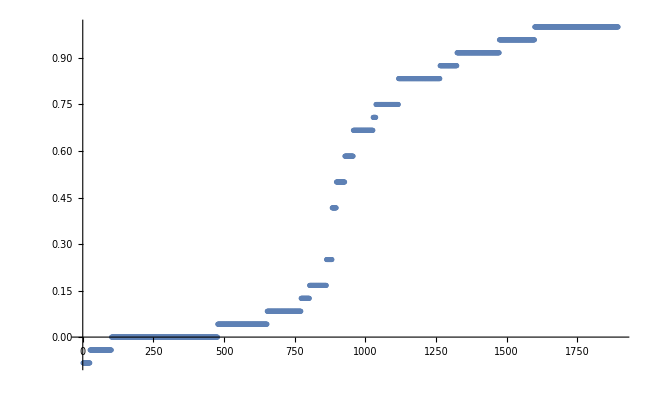

```mathematica
[Total[#]&,vectors]//Sort//ListPlot
```

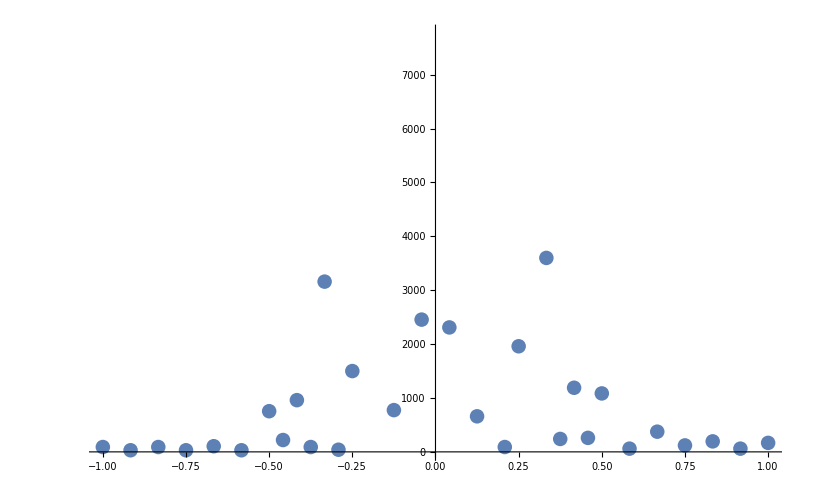

```mathematica
Sort[Tally[Flatten[vectors]],#1[[2]]>#2[[2]]&]//ListPlot
```

```mathematica
Sort[Tally[Flatten[vectors]],#1[[2]]>#2[[2]]&]
```

{{0,38853},{-1/6,9130},{-1/12,8945},{1/6,8640},{1/12,8375},{1/3,3600},{-1/3,3160},{-1/24,2455},{1/24,2310},{1/4,1960},{-1/4,1500},{5/12,1190},{1/2,1085},{-5/12,960},{-1/8,775},{-1/2,755},{1/8,660},{2/3,375},{11/24,260},{3/8,240},{-11/24,220},{5/6,195},{1,167},{3/4,120},{-2/3,105},{-3/8,90},{5/24,90},{-5/6,90},{-1,90},{7/12,60},{11/12,60},{-7/24,40},{-3/4,30},{-7/12,30},{-11/12,30}}